```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Documents/GitHub/two-point-correlators-with-masses/yukawa/3loop

```mathematica
<<LiteRed2`
(*<<Mint`*)
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Tue 1 Apr 2025 22:18:26
Read from:/Users/cesarecarlomella/Software/LiteRed2/LiteRed2025.m (CRC32:2902354241,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
Grid[{{"D1",k1^2-m^2,k1^2-m^2,k1^2-m^2},{"D2",k2^2-m^2,k2^2-m^2,k2^2-m^2},{"D3",k3^2-m^2,k3^2,k3^2},{"D4",(k1-p)^2-m^2,(k1-p)^2-m^2,(k1-p)^2-m^2},{"D5",(k2-p)^2-m^2,(k2-p)^2-m^2,(k2-p)^2-m^2},{"D6",(k3-p)^2-m^2,(k3-p)^2,(k3-p)^2},{"D7",(k1-k2)^2,(k1-k3)^2-m^2,(k1-k2)^2},{"D8",(k1-k3)^2,(k2-k3)^2-m^2,(k2+k3-p)^2-m^2},{"D9",(k2-k3)^2,(k1+k2-k3-p)^2,(k1+k3-p)^2-m^2}},Frame->All]
```

D1 | k1^2-m^2 | k1^2-m^2 | k1^2-m^2
D2 | k2^2-m^2 | k2^2-m^2 | k2^2-m^2
D3 | k3^2-m^2 | k3^2 | k3^2
D4 | -m^2+(k1-p)^2 | -m^2+(k1-p)^2 | -m^2+(k1-p)^2
D5 | -m^2+(k2-p)^2 | -m^2+(k2-p)^2 | -m^2+(k2-p)^2
D6 | -m^2+(k3-p)^2 | (k3-p)^2 | (k3-p)^2
D7 | (k1-k2)^2 | (k1-k3)^2-m^2 | (k1-k2)^2
D8 | (k1-k3)^2 | (k2-k3)^2-m^2 | -m^2+(k2+k3-p)^2
D9 | (k2-k3)^2 | (k1+k2-k3-p)^2 | -m^2+(k1+k3-p)^2

### Preliminaries

```mathematica
family = famA;
```

```mathematica
SetDim[d];
Declare[
{p,k1,k2,k3},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
intfam  = {-m2+sp[k1,k1],-m2+sp[k2,k2],-m2+sp[k3,k3],-m2+sp[k1,k1]-2 sp[k1,p]+sp[p,p],-m2+sp[k2,k2]-2 sp[k2,p]+sp[p,p],-m2+sp[k3,k3]-2 sp[k3,p]+sp[p,p],sp[k1,k1]-2 sp[k1,k2]+sp[k2,k2],sp[k1,k1]-2 sp[k1,k3]+sp[k3,k3],sp[k2,k2]-2 sp[k2,k3]+sp[k3,k3]}
```

{-m2+k1·k1,-m2+k2·k2,-m2+k3·k3,-m2+pp+k1·k1-2 k1·p,-m2+pp+k2·k2-2 k2·p,-m2+pp+k3·k3-2 k3·p,k1·k1-2 k1·k2+k2·k2,k1·k1-2 k1·k3+k3·k3,k2·k2-2 k2·k3+k3·k3}

```mathematica
(*(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family,intfam,{k1,k2,k3},Directory->"famA"]

GenerateIBP[family];

AnalyzeSectors[family];

FindSymmetries[family];

(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector/@UniqueSectors[family];*)

(*Save to disk*)
DiskSave[family];
```

```mathematica
Get["./famA/famA"];
```

```mathematica
MIs[family]
```

{j[famA,0,0,0,1,1,1,0,0,0],j[famA,0,0,0,0,1,1,1,1,0],j[famA,0,0,1,0,1,0,1,1,0],j[famA,0,0,2,0,1,0,1,1,0],j[famA,0,0,1,0,1,0,2,1,0],j[famA,0,0,1,1,1,0,0,0,1],j[famA,0,0,2,1,1,0,0,0,1],j[famA,0,0,1,1,1,1,0,0,0],j[famA,0,0,1,0,1,1,1,1,0],j[famA,0,0,1,1,1,0,0,1,1],j[famA,0,0,2,1,1,0,0,1,1],j[famA,0,0,1,2,1,0,0,1,1],j[famA,0,1,1,1,0,1,1,0,0],j[famA,0,2,1,1,0,1,1,0,0],j[famA,0,1,1,1,1,1,0,0,0],j[famA,0,1,1,0,1,1,1,1,0],j[famA,0,1,1,1,0,1,1,0,1],j[famA,1,1,1,1,1,1,0,0,0],j[famA,0,1,1,1,1,1,1,1,0],j[famA,0,2,1,1,1,1,1,1,0]}

```mathematica
MIs[family]
mis=MIs[family];
tomis=ToMIsRule[mis];
```

{j[famA,0,0,0,1,1,1,0,0,0],j[famA,0,0,0,0,1,1,1,1,0],j[famA,0,0,1,0,1,0,1,1,0],j[famA,0,0,2,0,1,0,1,1,0],j[famA,0,0,1,0,1,0,2,1,0],j[famA,0,0,1,1,1,0,0,0,1],j[famA,0,0,2,1,1,0,0,0,1],j[famA,0,0,1,1,1,1,0,0,0],j[famA,0,0,1,0,1,1,1,1,0],j[famA,0,0,1,1,1,0,0,1,1],j[famA,0,0,2,1,1,0,0,1,1],j[famA,0,0,1,2,1,0,0,1,1],j[famA,0,1,1,1,0,1,1,0,0],j[famA,0,2,1,1,0,1,1,0,0],j[famA,0,1,1,1,1,1,0,0,0],j[famA,0,1,1,0,1,1,1,1,0],j[famA,0,1,1,1,0,1,1,0,1],j[famA,1,1,1,1,1,1,0,0,0],j[famA,0,1,1,1,1,1,1,1,0],j[famA,0,2,1,1,1,1,1,1,0]}

```mathematica
(*LiteRed Masters*)
todiff= MIs[family];
```

```mathematica
(*diff eq for LiteRed Masters*)
derpp = Dinv[todiff,pp];
derm2 = Dinv[todiff,m2];
rhs=Union[Join[Union@Cases[derpp, j[family,a__],Infinity],Union@Cases[derm2, j[family,a__],Infinity]]];
rhsRed = Collect[IBPReduce[rhs],{_j}, Factor];
ReplaceRHS = Thread[Rule[rhs,rhsRed]];
redderpp=Collect[derpp/.ReplaceRHS, {_j},Factor];
redderm2=Collect[derm2/.ReplaceRHS, {_j},Factor];
MppLiteRed = CoefficientArrays[redderpp,todiff][[2]]//Normal;
Mm2LiteRed = CoefficientArrays[redderm2,todiff][[2]]//Normal;
```

```mathematica
(*MppLiteRed//MatrixPlot
Mm2LiteRed//MatrixPlot*)
```

```mathematica
Reverse[(todiff[[1,2;;]] /. j -> List) ]
```

{0,0,0,1,1,1,0,0,0}

```mathematica
Table[{todiff[[i]] /. 2-> 1,FromDigits[Reverse[(todiff[[i,2;;]]/. 2-> 1 /. j -> List) ],2], Total[todiff[[i,2;;]] /. 2-> 1/. j -> List]}, {i,1,Length[todiff]}]//TableForm
```

j[famA,0,0,0,1,1,1,0,0,0] | 56 | 3
j[famA,0,0,0,0,1,1,1,1,0] | 240 | 4
j[famA,0,0,1,0,1,0,1,1,0] | 212 | 4
j[famA,0,0,1,0,1,0,1,1,0] | 212 | 4
j[famA,0,0,1,0,1,0,1,1,0] | 212 | 4
j[famA,0,0,1,1,1,0,0,0,1] | 284 | 4
j[famA,0,0,1,1,1,0,0,0,1] | 284 | 4
j[famA,0,0,1,1,1,1,0,0,0] | 60 | 4
j[famA,0,0,1,0,1,1,1,1,0] | 244 | 5
j[famA,0,0,1,1,1,0,0,1,1] | 412 | 5
j[famA,0,0,1,1,1,0,0,1,1] | 412 | 5
j[famA,0,0,1,1,1,0,0,1,1] | 412 | 5
j[famA,0,1,1,1,0,1,1,0,0] | 110 | 5
j[famA,0,1,1,1,0,1,1,0,0] | 110 | 5
j[famA,0,1,1,1,1,1,0,0,0] | 62 | 5
j[famA,0,1,1,0,1,1,1,1,0] | 246 | 6
j[famA,0,1,1,1,0,1,1,0,1] | 366 | 6
j[famA,1,1,1,1,1,1,0,0,0] | 63 | 6
j[famA,0,1,1,1,1,1,1,1,0] | 254 | 7
j[famA,0,1,1,1,1,1,1,1,0] | 254 | 7

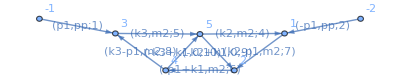

```mathematica
Import["./graphs/topoA/all/topoA_7_254.dot"]
```

```mathematica
j[famA,0,0,1,1,1,-1,0,1,1]//IBPReduce
```

((-2+d) j[famA,0,0,0,0,1,1,1,1,0])/(2 (-5+2 d))+((-2+d) j[famA,0,0,1,1,1,0,0,0,1])/(-5+2 d)+((-4 m2+d m2-3 pp+d pp) j[famA,0,0,1,1,1,0,0,1,1])/(-5+2 d)-(2 (2 m2^2+m2 pp) j[famA,0,0,1,2,1,0,0,1,1])/(-5+2 d)-(2 (m2^2-m2 pp) j[famA,0,0,2,1,1,0,0,1,1])/(-5+2 d)

### Start From d = 2

```mathematica
Dinv[j[famA,0,0,1,1,1,-1,0,1,1],pp] //IBPReduce
```

((16-14 d+3 d^2) j[famA,0,0,0,0,1,1,1,1,0])/(4 (-5+2 d) pp)+((-4+4 d-d^2) j[famA,0,0,1,1,1,0,0,0,1])/(2 (-5+2 d) pp)+((-8 m2+6 d m2-d^2 m2+24 pp-17 d pp+3 d^2 pp) j[famA,0,0,1,1,1,0,0,1,1])/(2 (-5+2 d) pp)+((-4 m2^2+2 d m2^2+8 m2 pp-3 d m2 pp) j[famA,0,0,1,2,1,0,0,1,1])/((-5+2 d) pp)+((-2 m2^2+d m2^2-3 m2 pp+d m2 pp) j[famA,0,0,2,1,1,0,0,1,1])/((-5+2 d) pp)

```mathematica
Length[todiff]
```

20

```mathematica
(*My Masters basis in d=2*)
mybasis= {(d-2)j[famA,0,0,0,1,1,1,0,0,0], (* tadpole ^ 3*)
 (-5+2 d)m2 j[famA,0,0,0,0,1,1,1,1,0], (* sunrise with two masses and no momentum *)
(* three MI sunrise*)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,0,1,0,1,1,0], (* banana with 2 equal masses *)
(d-2) j[famA,0,0,1,-1,1,0,1,1,0],
(d-2) j[famA,0,0,1,0,1,-1,1,1,0],
(* *)
(d-2)  j[famA,0,-1,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole *)
(d-2)Sqrt[pp] √(4 m2-pp) j[famA,0,0,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole *)
(* *)
(d-2)√pp √(4 m2-pp) j[famA,0,0,1,1,1,1,0,0,0], (* tadpole^2 * bubble *)
(* *)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,-1,1,1,1,1,0],
(* *)
(d-2)√(4m2-pp)Sqrt[pp]  j[famA,0,0,1,1,1,-1,0,1,1], (* triangle with two bubbles, 3 MIs*)
(d-2)((m2-pp)j[famA,0,0,1,1,1,0,-1,1,1]+2 (-m2+pp) j[famA,0,0,1,1,1,0,0,0,1]),
(d-2) (j[famA,0,0,1,1,1,-1,-1,1,1]+m2  j[famA,0,0,1,1,1,0,-1,1,1] -2 m2 j[famA,0,0,1,1,1,0,0,0,1]),
(* *)
(d-2)((4m2-pp) pp)j[famA,0,1,1,1,0,1,1,0,0],
(d-2)√(4m2-pp)Sqrt[pp] j[famA,0,1,1,1,-1,1,1,0,0],
(* *)
(d-2)pp(4m2-pp)j[famA,0,1,1,1,1,1,0,0,0],
(* *)
(d-2)(4 m2-pp) pp j[famA,0,1,1,0,1,1,1,1,-1],
(* *)
(d-2)m2 j[famA,0,1,1,1,-1,1,1,-1,1] + (-2+d) (2 m2-pp) j[famA,0,0,1,-1,1,1,1,1,0]+1/2 (-2+d) (-2 m2+pp) j[famA,0,0,1,0,1,0,1,1,0]-1/2 (-2+d) (-2 m2+pp) j[famA,0,0,1,1,1,0,0,0,1]-1/2 (-2+d)  (-2 m2+pp) j[famA,0,1,1,1,-1,1,1,0,0]+ (-7+2 d)/(2 (-3+d))(d-2)j[famA,0,0,0,1,1,1,0,0,0],
(* *)
(d-2)(4m2-pp )^(3/2)pp^(3/2) j[famA,1,1,1,1,1,1,0,0,0],
(*  the top sector has to be studied in d = 4 *)
j[famA,0,1,1,1,1,1,1,1,0],
  j[famA,1,1,1,1,1,1,1,1,0]};
(* my = T.LiteRed*)
T=CoefficientArrays[(IBPReduce[mybasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasis]//Together//Union;
```

```mathematica
(*T=T//Simplify//PowerExpand;*)
```

```mathematica
(*invT=Inverse[T]//Simplify;
invT=invT // PowerExpand;*)
```

```mathematica
(*derTpp = D[T,pp]//Simplify;
derTm2 = D[T,m2]//Simplify;*)
```

```mathematica
(*Mpp=(derTpp.invT//Simplify) + T.MppLiteRed.(invT)//PowerExpand//Simplify;
Mm2=(derTm2.invT//Simplify) + T.Mm2LiteRed.(invT)//PowerExpand//Simplify;*)
```

```mathematica
homT=T[[19;;20,19;;20]];
invhomT=Inverse[homT]//Simplify;
invhomT=invhomT // PowerExpand;
derhomTpp = D[homT,pp]//Simplify;
derhomTm2 = D[homT,m2]//Simplify;
Mpp=(derhomTpp.invhomT//Simplify) + homT.MppLiteRed[[19;;20,19;;20]].(invhomT)//PowerExpand//Simplify;
R2 = IdentityMatrix[2];
R2[[1,1]] =1
Mpptest=(D[R2,pp].Inverse[R2]//Simplify) + R2.Mpp.(Inverse[R2])//PowerExpand//Simplify;
```

1

```mathematica
Mpptest // MatrixForm
```

(-1/pp | 1/2 (-4+d)
(-4+d)/((4 m2-pp) pp) | -(12 m2-16 pp+3 d pp)/(8 m2 pp-2 pp^2))

```mathematica
Mpptest//MatrixForm
Mpptest/.d->4//Simplify//MatrixForm
```

(-1/pp | 1/2 (-4+d)
(-4+d)/((4 m2-pp) pp) | -(12 m2-16 pp+3 d pp)/(8 m2 pp-2 pp^2))

(-1/pp | 0
0 | (-6 m2+2 pp)/((4 m2-pp) pp))

```mathematica
E^(-Integrate[(-6 m2+2 pp)/((4 m2-pp) pp),pp])//Simplify
```

pp^(3/2) √(-4 m2+pp)

## Shift in d ~ 4

```mathematica
toshift ={j[famA,0,-1,1,1,1,0,0,0,1],j[famA,0,0,0,0,1,1,1,1,0],j[famA,0,0,0,1,1,1,0,0,0],j[famA,0,0,1,-1,1,0,1,1,0],j[famA,0,0,1,-1,1,1,1,1,0],j[famA,0,0,1,0,1,-1,1,1,0],j[famA,0,0,1,0,1,0,1,1,0],j[famA,0,0,1,1,1,-1,-1,1,1],j[famA,0,0,1,1,1,-1,0,1,1],j[famA,0,0,1,1,1,0,-1,1,1],j[famA,0,0,1,1,1,0,0,0,1],j[famA,0,0,1,1,1,1,0,0,0],j[famA,0,1,1,0,1,1,1,1,-1],j[famA,0,1,1,1,-1,1,1,-1,1],j[famA,0,1,1,1,-1,1,1,0,0],j[famA,0,1,1,1,0,1,1,0,0],j[famA,0,1,1,1,1,1,0,0,0],j[famA,1,1,1,1,1,1,0,0,0]};
toshift= toshift/. j[famA, a__] :> "topoA "<>StringReplace[StringReplace[StringReplace[ToString[{a}] , ","->""],"{"->""],"}"->""]
```

{topoA 0 -1 1 1 1 0 0 0 1,topoA 0 0 0 0 1 1 1 1 0,topoA 0 0 0 1 1 1 0 0 0,topoA 0 0 1 -1 1 0 1 1 0,topoA 0 0 1 -1 1 1 1 1 0,topoA 0 0 1 0 1 -1 1 1 0,topoA 0 0 1 0 1 0 1 1 0,topoA 0 0 1 1 1 -1 -1 1 1,topoA 0 0 1 1 1 -1 0 1 1,topoA 0 0 1 1 1 0 -1 1 1,topoA 0 0 1 1 1 0 0 0 1,topoA 0 0 1 1 1 1 0 0 0,topoA 0 1 1 0 1 1 1 1 -1,topoA 0 1 1 1 -1 1 1 -1 1,topoA 0 1 1 1 -1 1 1 0 0,topoA 0 1 1 1 0 1 1 0 0,topoA 0 1 1 1 1 1 0 0 0,topoA 1 1 1 1 1 1 0 0 0}

```mathematica
Close["tbshifted"]
Do[WriteLine["tbshifted", toshift[[i]]], {i,1,Length[toshift]}]
```

tbshifted

```mathematica
shifts=Import["./ints_dimshifted.m"]/. INT["topoAdimdec2",a__,{bin__}]:>j[famA, bin] /. INT["topoA",a__, {bin__}]:>j[famA,bin];
```

```mathematica
mybasisd4=mybasis/. d-> d-2/.shifts;
mybasisd4[[19]]=(d-4)^3(d-3)m2^3 j[famA,0,1,1,1,1,1,1,1,0]pp;
mybasisd4[[20]]=(d-4)^3(d-3)m2^3 j[famA,1,1,1,1,1,1,1,1,0] pp^(3/2) √(4 m2-pp);
mybasisd4 = mybasisd4/m2/m2/m2;
```

```mathematica
(* my = T.LiteRed*)
T=CoefficientArrays[(IBPReduce[mybasisd4]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasisd4]//Together//Union;
```

```mathematica
T=T//Simplify//PowerExpand;
```

```mathematica
Tsymb=T /.{ Sqrt[pp]-> sqrtpp, 1/Sqrt[pp]->sqrtpp/pp ,pp^(3/2) -> sqrtpp pp, 1/pp^(3/2) -> sqrtpp/pp/ pp ,Sqrt[(4 m2-pp)]->sqrt4m2, 1/Sqrt[(4 m2-pp)] -> sqrt4m2/(4m2 -pp) ,(4 m2-pp)^(5/2)->sqrt4m2 (4 m2 -pp)^2, 1/(4 m2-pp)^(5/2)->sqrt4m2/((4 m2-pp)^3),(4 m2-pp)^(3/2)->sqrt4m2 (4 m2-pp), 1/(4 m2-pp)^(3/2)->sqrt4m2 /((4 m2 -pp)^2)}//Simplify;
(*% /. sqrt4m2-> 0 /. sqrtpp ->0*)
```

```mathematica
<<FiniteFlow`
```

```mathematica
TinvSymb=FFInverse[Tsymb]// Simplify;
```

```mathematica
invT=TinvSymb /. sqrt4m2 ->Sqrt[4m2-pp] /. sqrtpp ->Sqrt[pp];
```

```mathematica
T.invT// Simplify
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
derTpp = D[T,pp]//Simplify;
derTm2 = D[T,m2]//Simplify;
```

```mathematica
Mpp=(derTpp.invT//Simplify) + T.MppLiteRed.(invT)//PowerExpand//Simplify;
Mm2=(derTm2.invT//Simplify) + T.Mm2LiteRed.(invT)//PowerExpand//Simplify;
```

```mathematica
(Integrate[Mm2 /(d-4) ,m2]//TrigToExp) /. _Log -> 0//Flatten //Union
(Integrate[Mpp /(d-4) ,pp]//TrigToExp) /. _Log -> 0//Flatten //Union
```

{0}

{0}

```mathematica
mybasisd4=Collect[mybasisd4, {_j},Simplify]
```

{(4-d) j[famA,0,0,0,2,2,2,0,0,0],(9-2 d) m2 j[famA,0,0,0,0,1,2,2,2,0]+(9-2 d) m2 j[famA,0,0,0,0,2,1,2,2,0]+(9-2 d) m2 j[famA,0,0,0,0,2,2,1,2,0]+(9-2 d) m2 j[famA,0,0,0,0,2,2,2,1,0],-((-4+d) √(4 m2-pp) √pp j[famA,0,0,1,0,2,0,2,2,0])-(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,0,1,0,2,2,0]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,0,2,0,1,2,0]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,0,2,0,2,1,0],(4-d) j[famA,0,0,1,-1,2,0,2,2,0]+(-4+d) j[famA,0,0,1,0,1,0,2,2,0]+(-4+d) j[famA,0,0,1,0,2,0,1,2,0]+(4-d) j[famA,0,0,2,-1,1,0,2,2,0]+(4-d) j[famA,0,0,2,-1,2,0,1,2,0]+(4-d) j[famA,0,0,2,-1,2,0,2,1,0]+(-4+d) j[famA,0,0,2,0,1,0,2,1,0]+(-4+d) j[famA,0,0,2,0,2,0,1,1,0],(-4+d) j[famA,0,0,1,0,1,0,2,2,0]+(4-d) j[famA,0,0,1,0,2,-1,2,2,0]+(-4+d) j[famA,0,0,1,0,2,0,1,2,0]+(-4+d) j[famA,0,0,1,0,2,0,2,1,0]+(4-d) j[famA,0,0,2,0,1,-1,2,2,0]+(4-d) j[famA,0,0,2,0,2,-1,1,2,0]+(4-d) j[famA,0,0,2,0,2,-1,2,1,0],(4-d) j[famA,0,-1,1,2,2,0,0,0,2]+(4-d) j[famA,0,-1,2,2,1,0,0,0,2]+(4-d) j[famA,0,-1,2,2,2,0,0,0,1]+(-4+d) j[famA,0,0,1,2,1,0,0,0,2]+(-4+d) j[famA,0,0,2,2,1,0,0,0,1],-((-4+d) √(4 m2-pp) √pp j[famA,0,0,1,2,2,0,0,0,2])-(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,2,1,0,0,0,2]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,2,2,0,0,0,1],-((-4+d) √(4 m2-pp) √pp j[famA,0,0,1,2,2,2,0,0,0])-(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,2,2,1,0,0,0],-((-4+d) √(4 m2-pp) √pp j[famA,0,0,1,-1,1,2,2,2,0])-(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,-1,2,1,2,2,0]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,-1,2,2,1,2,0]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,-1,2,2,2,1,0]+(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,0,1,1,2,2,0]+(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,0,1,2,2,1,0]+(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,0,2,1,1,2,0]+(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,0,2,2,1,1,0]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,-1,1,1,2,2,0]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,-1,2,1,1,2,0]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,-1,2,1,2,1,0]+(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,0,1,1,2,1,0]+(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,0,2,1,1,1,0],(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,1,1,0,0,2,2]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,1,2,-1,0,2,2]+(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,1,2,0,0,2,1]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,2,1,-1,0,2,2]+(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,2,1,0,0,1,2]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,2,2,-1,0,1,2]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,2,2,-1,0,2,1]+(-4+d) √(4 m2-pp) √pp j[famA,0,0,1,2,2,0,0,1,1]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,1,1,-1,0,2,2]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,1,2,-1,0,2,1]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,2,1,-1,0,1,2]-(-4+d) √(4 m2-pp) √pp j[famA,0,0,2,2,2,-1,0,1,1],-((-4+d) (m2-pp) j[famA,0,0,1,1,2,0,-1,2,2])+(-4+d) (m2-pp) j[famA,0,0,1,1,2,0,0,1,2]+(-4+d) (m2-pp) j[famA,0,0,1,1,2,0,0,2,1]-(-4+d) (m2-pp) j[famA,0,0,1,2,1,0,-1,2,2]+(-4+d) (m2-pp) j[famA,0,0,1,2,1,0,0,1,2]+(-4+d) (m2-pp) j[famA,0,0,1,2,1,0,0,2,1]-(-4+d) (m2-pp) j[famA,0,0,1,2,2,0,-1,1,2]-(-4+d) (m2-pp) j[famA,0,0,1,2,2,0,-1,2,1]+2 (-4+d) (m2-pp) j[famA,0,0,1,2,2,0,0,0,2]-(-4+d) (m2-pp) j[famA,0,0,2,1,1,0,-1,2,2]+(-4+d) (m2-pp) j[famA,0,0,2,1,1,0,0,1,2]+(-4+d) (m2-pp) j[famA,0,0,2,1,1,0,0,2,1]-(-4+d) (m2-pp) j[famA,0,0,2,1,2,0,-1,2,1]+(-4+d) (m2-pp) j[famA,0,0,2,1,2,0,0,1,1]-(-4+d) (m2-pp) j[famA,0,0,2,2,1,0,-1,1,2]+2 (-4+d) (m2-pp) j[famA,0,0,2,2,1,0,0,0,2]+(-4+d) (m2-pp) j[famA,0,0,2,2,1,0,0,1,1]-(-4+d) (m2-pp) j[famA,0,0,2,2,2,0,-1,1,1]+2 (-4+d) (m2-pp) j[famA,0,0,2,2,2,0,0,0,1],(-4+d) j[famA,0,0,1,1,1,0,-1,2,2]+(4-d) j[famA,0,0,1,1,1,0,0,1,2]+(4-d) j[famA,0,0,1,1,1,0,0,2,1]+(4-d) j[famA,0,0,1,1,2,-1,-1,2,2]+(-4+d) j[famA,0,0,1,1,2,-1,0,1,2]+(-4+d) j[famA,0,0,1,1,2,-1,0,2,1]+(-4+d) j[famA,0,0,1,1,2,0,-1,2,1]-(-4+d) m2 j[famA,0,0,1,1,2,0,-1,2,2]+(4-d) j[famA,0,0,1,1,2,0,0,1,1]+(-4+d) m2 j[famA,0,0,1,1,2,0,0,1,2]+(-4+d) m2 j[famA,0,0,1,1,2,0,0,2,1]+(4-d) j[famA,0,0,1,2,1,-1,-1,2,2]+(-4+d) j[famA,0,0,1,2,1,-1,0,1,2]+(-4+d) j[famA,0,0,1,2,1,-1,0,2,1]+(-4+d) j[famA,0,0,1,2,1,0,-1,1,2]-(-4+d) m2 j[famA,0,0,1,2,1,0,-1,2,2]+(4-d) j[famA,0,0,1,2,1,0,0,1,1]+(-4+d) m2 j[famA,0,0,1,2,1,0,0,1,2]+(-4+d) m2 j[famA,0,0,1,2,1,0,0,2,1]+(4-d) j[famA,0,0,1,2,2,-1,-1,1,2]+(4-d) j[famA,0,0,1,2,2,-1,-1,2,1]+(-4+d) j[famA,0,0,1,2,2,0,-1,1,1]-(-4+d) m2 j[famA,0,0,1,2,2,0,-1,1,2]-(-4+d) m2 j[famA,0,0,1,2,2,0,-1,2,1]+2 (-4+d) m2 j[famA,0,0,1,2,2,0,0,0,2]+(4-d) j[famA,0,0,2,1,1,-1,-1,2,2]+(-4+d) j[famA,0,0,2,1,1,-1,0,1,2]+(-4+d) j[famA,0,0,2,1,1,-1,0,2,1]-(-4+d) m2 j[famA,0,0,2,1,1,0,-1,2,2]+(-4+d) m2 j[famA,0,0,2,1,1,0,0,1,2]+(-4+d) m2 j[famA,0,0,2,1,1,0,0,2,1]+(4-d) j[famA,0,0,2,1,2,-1,-1,2,1]+(-4+d) j[famA,0,0,2,1,2,-1,0,1,1]-(-4+d) m2 j[famA,0,0,2,1,2,0,-1,2,1]+(-4+d) m2 j[famA,0,0,2,1,2,0,0,1,1]+(4-d) j[famA,0,0,2,2,1,-1,-1,1,2]+(-4+d) j[famA,0,0,2,2,1,-1,0,1,1]-(-4+d) m2 j[famA,0,0,2,2,1,0,-1,1,2]+2 (-4+d) m2 j[famA,0,0,2,2,1,0,0,0,2]+(-4+d) m2 j[famA,0,0,2,2,1,0,0,1,1]+(4-d) j[famA,0,0,2,2,2,-1,-1,1,1]-(-4+d) m2 j[famA,0,0,2,2,2,0,-1,1,1]+2 (-4+d) m2 j[famA,0,0,2,2,2,0,0,0,1],-((-4+d) (4 m2-pp) pp j[famA,0,1,1,2,0,2,2,0,0])-(-4+d) (4 m2-pp) pp j[famA,0,1,2,2,0,1,2,0,0]-(-4+d) (4 m2-pp) pp j[famA,0,2,1,1,0,2,2,0,0]-(-4+d) (4 m2-pp) pp j[famA,0,2,1,2,0,2,1,0,0]-(-4+d) (4 m2-pp) pp j[famA,0,2,2,1,0,1,2,0,0]-(-4+d) (4 m2-pp) pp j[famA,0,2,2,2,0,1,1,0,0],(-4+d) √(4 m2-pp) √pp j[famA,0,1,1,1,0,2,2,0,0]-(-4+d) √(4 m2-pp) √pp j[famA,0,1,1,2,-1,2,2,0,0]+(-4+d) √(4 m2-pp) √pp j[famA,0,1,1,2,0,2,1,0,0]+(-4+d) √(4 m2-pp) √pp j[famA,0,1,2,1,0,1,2,0,0]-(-4+d) √(4 m2-pp) √pp j[famA,0,1,2,2,-1,1,2,0,0]+(-4+d) √(4 m2-pp) √pp j[famA,0,1,2,2,0,1,1,0,0]-(-4+d) √(4 m2-pp) √pp j[famA,0,2,1,1,-1,2,2,0,0]-(-4+d) √(4 m2-pp) √pp j[famA,0,2,1,2,-1,2,1,0,0]-(-4+d) √(4 m2-pp) √pp j[famA,0,2,2,1,-1,1,2,0,0]-(-4+d) √(4 m2-pp) √pp j[famA,0,2,2,2,-1,1,1,0,0],-((-4+d) (4 m2-pp) pp j[famA,0,1,1,2,2,2,0,0,0])-(-4+d) (4 m2-pp) pp j[famA,0,1,2,2,2,1,0,0,0]-(-4+d) (4 m2-pp) pp j[famA,0,2,1,2,1,2,0,0,0]-(-4+d) (4 m2-pp) pp j[famA,0,2,2,2,1,1,0,0,0],(-4+d) (4 m2-pp) pp j[famA,0,1,1,0,1,2,1,2,0]+(-4+d) (4 m2-pp) pp j[famA,0,1,1,0,1,2,2,1,0]-(-4+d) (4 m2-pp) pp j[famA,0,1,1,0,1,2,2,2,-1]+(-4+d) (4 m2-pp) pp j[famA,0,1,1,0,2,1,1,2,0]+(-4+d) (4 m2-pp) pp j[famA,0,1,1,0,2,1,2,1,0]-(-4+d) (4 m2-pp) pp j[famA,0,1,1,0,2,1,2,2,-1]-(-4+d) (4 m2-pp) pp j[famA,0,1,1,0,2,2,1,2,-1]-(-4+d) (4 m2-pp) pp j[famA,0,1,1,0,2,2,2,1,-1]+(-4+d) (4 m2-pp) pp j[famA,0,1,2,0,1,1,1,2,0]+(-4+d) (4 m2-pp) pp j[famA,0,1,2,0,1,1,2,1,0]-(-4+d) (4 m2-pp) pp j[famA,0,1,2,0,1,1,2,2,-1]-(-4+d) (4 m2-pp) pp j[famA,0,1,2,0,2,1,1,2,-1]-(-4+d) (4 m2-pp) pp j[famA,0,1,2,0,2,1,2,1,-1]+(-4+d) (4 m2-pp) pp j[famA,0,2,1,0,1,1,1,2,0]+(-4+d) (4 m2-pp) pp j[famA,0,2,1,0,1,1,2,1,0]-(-4+d) (4 m2-pp) pp j[famA,0,2,1,0,1,1,2,2,-1]-(-4+d) (4 m2-pp) pp j[famA,0,2,1,0,1,2,1,2,-1]-(-4+d) (4 m2-pp) pp j[famA,0,2,1,0,1,2,2,1,-1]-(-4+d) (4 m2-pp) pp j[famA,0,2,2,0,1,1,1,2,-1]-(-4+d) (4 m2-pp) pp j[famA,0,2,2,0,1,1,2,1,-1],-((-4+d) (-11+2 d) j[famA,0,0,0,2,2,2,0,0,0])/(2 (-5+d))-(-4+d) (2 m2-pp) j[famA,0,0,1,-1,1,2,2,2,0]-(-4+d) (2 m2-pp) j[famA,0,0,1,-1,2,1,2,2,0]-(-4+d) (2 m2-pp) j[famA,0,0,1,-1,2,2,1,2,0]-(-4+d) (2 m2-pp) j[famA,0,0,1,-1,2,2,2,1,0]+(-4+d) (2 m2-pp) j[famA,0,0,1,0,1,1,2,2,0]+(-4+d) (2 m2-pp) j[famA,0,0,1,0,1,2,2,1,0]+1/2 (-4+d) (2 m2-pp) j[famA,0,0,1,0,2,0,2,2,0]+(-4+d) (2 m2-pp) j[famA,0,0,1,0,2,1,1,2,0]+(-4+d) (2 m2-pp) j[famA,0,0,1,0,2,2,1,1,0]+1/2 (-4+d) (-2 m2+pp) j[famA,0,0,1,2,2,0,0,0,2]-(-4+d) (2 m2-pp) j[famA,0,0,2,-1,1,1,2,2,0]-(-4+d) (2 m2-pp) j[famA,0,0,2,-1,2,1,1,2,0]-(-4+d) (2 m2-pp) j[famA,0,0,2,-1,2,1,2,1,0]+1/2 (-4+d) (2 m2-pp) j[famA,0,0,2,0,1,0,2,2,0]+(-4+d) (2 m2-pp) j[famA,0,0,2,0,1,1,2,1,0]+1/2 (-4+d) (2 m2-pp) j[famA,0,0,2,0,2,0,1,2,0]+1/2 (-4+d) (2 m2-pp) j[famA,0,0,2,0,2,0,2,1,0]+(-4+d) (2 m2-pp) j[famA,0,0,2,0,2,1,1,1,0]+1/2 (-4+d) (-2 m2+pp) j[famA,0,0,2,2,1,0,0,0,2]+1/2 (-4+d) (-2 m2+pp) j[famA,0,0,2,2,2,0,0,0,1]+(-4+d) m2 j[famA,0,1,1,1,-1,2,1,0,2]-(-4+d) m2 j[famA,0,1,1,1,-1,2,2,-1,2]+(-4+d) m2 j[famA,0,1,1,1,-1,2,2,0,1]-(-4+d) m2 j[famA,0,1,1,1,0,1,1,0,2]+(-4+d) m2 j[famA,0,1,1,1,0,1,2,-1,2]-(-4+d) m2 j[famA,0,1,1,1,0,1,2,0,1]-(-4+d) m2 j[famA,0,1,1,1,0,2,1,0,1]+(-4+d) m2 j[famA,0,1,1,1,0,2,2,-1,1]+1/2 (-4+d) (2 m2-pp) j[famA,0,1,1,1,0,2,2,0,0]+(-4+d) m2 j[famA,0,1,1,2,-1,1,1,0,2]-(-4+d) m2 j[famA,0,1,1,2,-1,1,2,-1,2]+(-4+d) m2 j[famA,0,1,1,2,-1,1,2,0,1]-(-4+d) m2 j[famA,0,1,1,2,-1,2,1,-1,2]-(-4+d) m2 j[famA,0,1,1,2,-1,2,2,-1,1]+1/2 (-4+d) (-2 m2+pp) j[famA,0,1,1,2,-1,2,2,0,0]+(-4+d) m2 j[famA,0,1,1,2,0,1,1,-1,2]-(-4+d) m2 j[famA,0,1,1,2,0,1,1,0,1]+(-4+d) m2 j[famA,0,1,1,2,0,2,1,-1,1]+1/2 (-4+d) (2 m2-pp) j[famA,0,1,1,2,0,2,1,0,0]+(-4+d) m2 j[famA,0,1,2,1,-1,1,1,0,2]-(-4+d) m2 j[famA,0,1,2,1,-1,1,2,-1,2]+(-4+d) m2 j[famA,0,1,2,1,-1,1,2,0,1]-(-4+d) m2 j[famA,0,1,2,1,0,1,1,0,1]+(-4+d) m2 j[famA,0,1,2,1,0,1,2,-1,1]+1/2 (-4+d) (2 m2-pp) j[famA,0,1,2,1,0,1,2,0,0]-(-4+d) m2 j[famA,0,1,2,2,-1,1,1,-1,2]-(-4+d) m2 j[famA,0,1,2,2,-1,1,2,-1,1]+1/2 (-4+d) (-2 m2+pp) j[famA,0,1,2,2,-1,1,2,0,0]+(-4+d) m2 j[famA,0,1,2,2,0,1,1,-1,1]+1/2 (-4+d) (2 m2-pp) j[famA,0,1,2,2,0,1,1,0,0]+(-4+d) m2 j[famA,0,2,1,1,-1,1,1,0,2]-(-4+d) m2 j[famA,0,2,1,1,-1,1,2,-1,2]+(-4+d) m2 j[famA,0,2,1,1,-1,1,2,0,1]+(-4+d) m2 j[famA,0,2,1,1,-1,2,1,0,1]-(-4+d) m2 j[famA,0,2,1,1,-1,2,2,-1,1]+1/2 (-4+d) (-2 m2+pp) j[famA,0,2,1,1,-1,2,2,0,0]-(-4+d) m2 j[famA,0,2,1,2,-1,1,1,-1,2]+(-4+d) m2 j[famA,0,2,1,2,-1,1,1,0,1]-(-4+d) m2 j[famA,0,2,1,2,-1,2,1,-1,1]+1/2 (-4+d) (-2 m2+pp) j[famA,0,2,1,2,-1,2,1,0,0]+(-4+d) m2 j[famA,0,2,2,1,-1,1,1,0,1]-(-4+d) m2 j[famA,0,2,2,1,-1,1,2,-1,1]+1/2 (-4+d) (-2 m2+pp) j[famA,0,2,2,1,-1,1,2,0,0]-(-4+d) m2 j[famA,0,2,2,2,-1,1,1,-1,1]+1/2 (-4+d) (-2 m2+pp) j[famA,0,2,2,2,-1,1,1,0,0],-((-4+d) (4 m2-pp)^(3/2) pp^(3/2) j[famA,1,1,1,2,2,2,0,0,0])-(-4+d) (4 m2-pp)^(3/2) pp^(3/2) j[famA,1,1,2,2,2,1,0,0,0]-(-4+d) (4 m2-pp)^(3/2) pp^(3/2) j[famA,1,2,1,2,1,2,0,0,0]-(-4+d) (4 m2-pp)^(3/2) pp^(3/2) j[famA,1,2,2,2,1,1,0,0,0]-(-4+d) (4 m2-pp)^(3/2) pp^(3/2) j[famA,2,1,1,1,2,2,0,0,0]-(-4+d) (4 m2-pp)^(3/2) pp^(3/2) j[famA,2,1,2,1,2,1,0,0,0]-(-4+d) (4 m2-pp)^(3/2) pp^(3/2) j[famA,2,2,1,1,1,2,0,0,0]-(-4+d) (4 m2-pp)^(3/2) pp^(3/2) j[famA,2,2,2,1,1,1,0,0,0],(-4+d)^3 (-3+d) pp j[famA,0,1,1,1,1,1,1,1,0],(-4+d)^3 (-3+d) √(4 m2-pp) pp^(3/2) j[famA,1,1,1,1,1,1,1,1,0]}

{-((-4+d) j[famA,0,0,0,2,2,2,0,0,0]),1/m2^2(-5+2 (-2+d)) (-m2^3 j[famA,0,0,0,0,1,2,2,2,0]-m2^3 j[famA,0,0,0,0,2,1,2,2,0]-m2^3 j[famA,0,0,0,0,2,2,1,2,0]-m2^3 j[famA,0,0,0,0,2,2,2,1,0]),1/m2^3(-4+d) √(4 m2-pp) √pp (-m2^3 j[famA,0,0,1,0,2,0,2,2,0]-m2^3 j[famA,0,0,2,0,1,0,2,2,0]-m2^3 j[famA,0,0,2,0,2,0,1,2,0]-m2^3 j[famA,0,0,2,0,2,0,2,1,0]),1/m2^3(-4+d) (-m2^3 j[famA,0,0,1,-1,2,0,2,2,0]+m2^3 j[famA,0,0,1,0,1,0,2,2,0]+m2^3 j[famA,0,0,1,0,2,0,1,2,0]-m2^3 j[famA,0,0,2,-1,1,0,2,2,0]-m2^3 j[famA,0,0,2,-1,2,0,1,2,0]-m2^3 j[famA,0,0,2,-1,2,0,2,1,0]+m2^3 j[famA,0,0,2,0,1,0,2,1,0]+m2^3 j[famA,0,0,2,0,2,0,1,1,0]),1/m2^3(-4+d) (m2^3 j[famA,0,0,1,0,1,0,2,2,0]-m2^3 j[famA,0,0,1,0,2,-1,2,2,0]+m2^3 j[famA,0,0,1,0,2,0,1,2,0]+m2^3 j[famA,0,0,1,0,2,0,2,1,0]-m2^3 j[famA,0,0,2,0,1,-1,2,2,0]-m2^3 j[famA,0,0,2,0,2,-1,1,2,0]-m2^3 j[famA,0,0,2,0,2,-1,2,1,0]),1/m2^3(-4+d) (-m2^3 j[famA,0,-1,1,2,2,0,0,0,2]-m2^3 j[famA,0,-1,2,2,1,0,0,0,2]-m2^3 j[famA,0,-1,2,2,2,0,0,0,1]+m2^3 j[famA,0,0,1,2,1,0,0,0,2]+m2^3 j[famA,0,0,2,2,1,0,0,0,1]),((-4+d) √(4 m2-pp) √pp (-m2^3 j[famA,0,0,1,2,2,0,0,0,2]-m2^3 j[famA,0,0,2,2,1,0,0,0,2]-m2^3 j[famA,0,0,2,2,2,0,0,0,1]))/m2^3,((-4+d) √(4 m2-pp) √pp (-m2^3 j[famA,0,0,1,2,2,2,0,0,0]-m2^3 j[famA,0,0,2,2,2,1,0,0,0]))/m2^3,1/m2^3(-4+d) √(4 m2-pp) √pp (-m2^3 j[famA,0,0,1,-1,1,2,2,2,0]-m2^3 j[famA,0,0,1,-1,2,1,2,2,0]-m2^3 j[famA,0,0,1,-1,2,2,1,2,0]-m2^3 j[famA,0,0,1,-1,2,2,2,1,0]+m2^3 j[famA,0,0,1,0,1,1,2,2,0]+m2^3 j[famA,0,0,1,0,1,2,2,1,0]+m2^3 j[famA,0,0,1,0,2,1,1,2,0]+m2^3 j[famA,0,0,1,0,2,2,1,1,0]-m2^3 j[famA,0,0,2,-1,1,1,2,2,0]-m2^3 j[famA,0,0,2,-1,2,1,1,2,0]-m2^3 j[famA,0,0,2,-1,2,1,2,1,0]+m2^3 j[famA,0,0,2,0,1,1,2,1,0]+m2^3 j[famA,0,0,2,0,2,1,1,1,0]),1/m2^3(-4+d) √(4 m2-pp) √pp (m2^3 j[famA,0,0,1,1,1,0,0,2,2]-m2^3 j[famA,0,0,1,1,2,-1,0,2,2]+m2^3 j[famA,0,0,1,1,2,0,0,2,1]-m2^3 j[famA,0,0,1,2,1,-1,0,2,2]+m2^3 j[famA,0,0,1,2,1,0,0,1,2]-m2^3 j[famA,0,0,1,2,2,-1,0,1,2]-m2^3 j[famA,0,0,1,2,2,-1,0,2,1]+m2^3 j[famA,0,0,1,2,2,0,0,1,1]-m2^3 j[famA,0,0,2,1,1,-1,0,2,2]-m2^3 j[famA,0,0,2,1,2,-1,0,2,1]-m2^3 j[famA,0,0,2,2,1,-1,0,1,2]-m2^3 j[famA,0,0,2,2,2,-1,0,1,1]),1/m2^3(-4+d) ((m2-pp) (-m2^3 j[famA,0,0,1,1,2,0,-1,2,2]+m2^3 j[famA,0,0,1,1,2,0,0,1,2]+m2^3 j[famA,0,0,1,1,2,0,0,2,1]-m2^3 j[famA,0,0,1,2,1,0,-1,2,2]+m2^3 j[famA,0,0,1,2,1,0,0,1,2]+m2^3 j[famA,0,0,1,2,1,0,0,2,1]-m2^3 j[famA,0,0,1,2,2,0,-1,1,2]-m2^3 j[famA,0,0,1,2,2,0,-1,2,1]-m2^3 j[famA,0,0,2,1,1,0,-1,2,2]+m2^3 j[famA,0,0,2,1,1,0,0,1,2]+m2^3 j[famA,0,0,2,1,1,0,0,2,1]-m2^3 j[famA,0,0,2,1,2,0,-1,2,1]+m2^3 j[famA,0,0,2,1,2,0,0,1,1]-m2^3 j[famA,0,0,2,2,1,0,-1,1,2]+m2^3 j[famA,0,0,2,2,1,0,0,1,1]-m2^3 j[famA,0,0,2,2,2,0,-1,1,1])+2 (-m2+pp) (-m2^3 j[famA,0,0,1,2,2,0,0,0,2]-m2^3 j[famA,0,0,2,2,1,0,0,0,2]-m2^3 j[famA,0,0,2,2,2,0,0,0,1])),1/m2^3(-4+d) (m2^3 j[famA,0,0,1,1,1,0,-1,2,2]-m2^3 j[famA,0,0,1,1,1,0,0,1,2]-m2^3 j[famA,0,0,1,1,1,0,0,2,1]-m2^3 j[famA,0,0,1,1,2,-1,-1,2,2]+m2^3 j[famA,0,0,1,1,2,-1,0,1,2]+m2^3 j[famA,0,0,1,1,2,-1,0,2,1]+m2^3 j[famA,0,0,1,1,2,0,-1,2,1]-m2^3 j[famA,0,0,1,1,2,0,0,1,1]-m2^3 j[famA,0,0,1,2,1,-1,-1,2,2]+m2^3 j[famA,0,0,1,2,1,-1,0,1,2]+m2^3 j[famA,0,0,1,2,1,-1,0,2,1]+m2^3 j[famA,0,0,1,2,1,0,-1,1,2]-m2^3 j[famA,0,0,1,2,1,0,0,1,1]-m2^3 j[famA,0,0,1,2,2,-1,-1,1,2]-m2^3 j[famA,0,0,1,2,2,-1,-1,2,1]+m2^3 j[famA,0,0,1,2,2,0,-1,1,1]-m2^3 j[famA,0,0,2,1,1,-1,-1,2,2]+m2^3 j[famA,0,0,2,1,1,-1,0,1,2]+m2^3 j[famA,0,0,2,1,1,-1,0,2,1]-m2^3 j[famA,0,0,2,1,2,-1,-1,2,1]+m2^3 j[famA,0,0,2,1,2,-1,0,1,1]-m2^3 j[famA,0,0,2,2,1,-1,-1,1,2]+m2^3 j[famA,0,0,2,2,1,-1,0,1,1]-m2^3 j[famA,0,0,2,2,2,-1,-1,1,1]+m2 (-m2^3 j[famA,0,0,1,1,2,0,-1,2,2]+m2^3 j[famA,0,0,1,1,2,0,0,1,2]+m2^3 j[famA,0,0,1,1,2,0,0,2,1]-m2^3 j[famA,0,0,1,2,1,0,-1,2,2]+m2^3 j[famA,0,0,1,2,1,0,0,1,2]+m2^3 j[famA,0,0,1,2,1,0,0,2,1]-m2^3 j[famA,0,0,1,2,2,0,-1,1,2]-m2^3 j[famA,0,0,1,2,2,0,-1,2,1]-m2^3 j[famA,0,0,2,1,1,0,-1,2,2]+m2^3 j[famA,0,0,2,1,1,0,0,1,2]+m2^3 j[famA,0,0,2,1,1,0,0,2,1]-m2^3 j[famA,0,0,2,1,2,0,-1,2,1]+m2^3 j[famA,0,0,2,1,2,0,0,1,1]-m2^3 j[famA,0,0,2,2,1,0,-1,1,2]+m2^3 j[famA,0,0,2,2,1,0,0,1,1]-m2^3 j[famA,0,0,2,2,2,0,-1,1,1])-2 m2 (-m2^3 j[famA,0,0,1,2,2,0,0,0,2]-m2^3 j[famA,0,0,2,2,1,0,0,0,2]-m2^3 j[famA,0,0,2,2,2,0,0,0,1])),1/m2^3(-4+d) (4 m2-pp) pp (-m2^3 j[famA,0,1,1,2,0,2,2,0,0]-m2^3 j[famA,0,1,2,2,0,1,2,0,0]-m2^3 j[famA,0,2,1,1,0,2,2,0,0]-m2^3 j[famA,0,2,1,2,0,2,1,0,0]-m2^3 j[famA,0,2,2,1,0,1,2,0,0]-m2^3 j[famA,0,2,2,2,0,1,1,0,0]),1/m2^3(-4+d) √(4 m2-pp) √pp (m2^3 j[famA,0,1,1,1,0,2,2,0,0]-m2^3 j[famA,0,1,1,2,-1,2,2,0,0]+m2^3 j[famA,0,1,1,2,0,2,1,0,0]+m2^3 j[famA,0,1,2,1,0,1,2,0,0]-m2^3 j[famA,0,1,2,2,-1,1,2,0,0]+m2^3 j[famA,0,1,2,2,0,1,1,0,0]-m2^3 j[famA,0,2,1,1,-1,2,2,0,0]-m2^3 j[famA,0,2,1,2,-1,2,1,0,0]-m2^3 j[famA,0,2,2,1,-1,1,2,0,0]-m2^3 j[famA,0,2,2,2,-1,1,1,0,0]),1/m2^3(-4+d) (4 m2-pp) pp (-m2^3 j[famA,0,1,1,2,2,2,0,0,0]-m2^3 j[famA,0,1,2,2,2,1,0,0,0]-m2^3 j[famA,0,2,1,2,1,2,0,0,0]-m2^3 j[famA,0,2,2,2,1,1,0,0,0]),1/m2^3(-4+d) (4 m2-pp) pp (m2^3 j[famA,0,1,1,0,1,2,1,2,0]+m2^3 j[famA,0,1,1,0,1,2,2,1,0]-m2^3 j[famA,0,1,1,0,1,2,2,2,-1]+m2^3 j[famA,0,1,1,0,2,1,1,2,0]+m2^3 j[famA,0,1,1,0,2,1,2,1,0]-m2^3 j[famA,0,1,1,0,2,1,2,2,-1]-m2^3 j[famA,0,1,1,0,2,2,1,2,-1]-m2^3 j[famA,0,1,1,0,2,2,2,1,-1]+m2^3 j[famA,0,1,2,0,1,1,1,2,0]+m2^3 j[famA,0,1,2,0,1,1,2,1,0]-m2^3 j[famA,0,1,2,0,1,1,2,2,-1]-m2^3 j[famA,0,1,2,0,2,1,1,2,-1]-m2^3 j[famA,0,1,2,0,2,1,2,1,-1]+m2^3 j[famA,0,2,1,0,1,1,1,2,0]+m2^3 j[famA,0,2,1,0,1,1,2,1,0]-m2^3 j[famA,0,2,1,0,1,1,2,2,-1]-m2^3 j[famA,0,2,1,0,1,2,1,2,-1]-m2^3 j[famA,0,2,1,0,1,2,2,1,-1]-m2^3 j[famA,0,2,2,0,1,1,1,2,-1]-m2^3 j[famA,0,2,2,0,1,1,2,1,-1]),1/m2^3(-((-7+2 (-2+d)) (-4+d) m2^3 j[famA,0,0,0,2,2,2,0,0,0])/(2 (-5+d))+1/2 (-4+d) (-2 m2+pp) (-m2^3 j[famA,0,0,1,0,2,0,2,2,0]-m2^3 j[famA,0,0,2,0,1,0,2,2,0]-m2^3 j[famA,0,0,2,0,2,0,1,2,0]-m2^3 j[famA,0,0,2,0,2,0,2,1,0])+(-4+d) (2 m2-pp) (-m2^3 j[famA,0,0,1,-1,1,2,2,2,0]-m2^3 j[famA,0,0,1,-1,2,1,2,2,0]-m2^3 j[famA,0,0,1,-1,2,2,1,2,0]-m2^3 j[famA,0,0,1,-1,2,2,2,1,0]+m2^3 j[famA,0,0,1,0,1,1,2,2,0]+m2^3 j[famA,0,0,1,0,1,2,2,1,0]+m2^3 j[famA,0,0,1,0,2,1,1,2,0]+m2^3 j[famA,0,0,1,0,2,2,1,1,0]-m2^3 j[famA,0,0,2,-1,1,1,2,2,0]-m2^3 j[famA,0,0,2,-1,2,1,1,2,0]-m2^3 j[famA,0,0,2,-1,2,1,2,1,0]+m2^3 j[famA,0,0,2,0,1,1,2,1,0]+m2^3 j[famA,0,0,2,0,2,1,1,1,0])-1/2 (-4+d) (-2 m2+pp) (-m2^3 j[famA,0,0,1,2,2,0,0,0,2]-m2^3 j[famA,0,0,2,2,1,0,0,0,2]-m2^3 j[famA,0,0,2,2,2,0,0,0,1])+(-4+d) m2 (m2^3 j[famA,0,1,1,1,-1,2,1,0,2]-m2^3 j[famA,0,1,1,1,-1,2,2,-1,2]+m2^3 j[famA,0,1,1,1,-1,2,2,0,1]-m2^3 j[famA,0,1,1,1,0,1,1,0,2]+m2^3 j[famA,0,1,1,1,0,1,2,-1,2]-m2^3 j[famA,0,1,1,1,0,1,2,0,1]-m2^3 j[famA,0,1,1,1,0,2,1,0,1]+m2^3 j[famA,0,1,1,1,0,2,2,-1,1]+m2^3 j[famA,0,1,1,2,-1,1,1,0,2]-m2^3 j[famA,0,1,1,2,-1,1,2,-1,2]+m2^3 j[famA,0,1,1,2,-1,1,2,0,1]-m2^3 j[famA,0,1,1,2,-1,2,1,-1,2]-m2^3 j[famA,0,1,1,2,-1,2,2,-1,1]+m2^3 j[famA,0,1,1,2,0,1,1,-1,2]-m2^3 j[famA,0,1,1,2,0,1,1,0,1]+m2^3 j[famA,0,1,1,2,0,2,1,-1,1]+m2^3 j[famA,0,1,2,1,-1,1,1,0,2]-m2^3 j[famA,0,1,2,1,-1,1,2,-1,2]+m2^3 j[famA,0,1,2,1,-1,1,2,0,1]-m2^3 j[famA,0,1,2,1,0,1,1,0,1]+m2^3 j[famA,0,1,2,1,0,1,2,-1,1]-m2^3 j[famA,0,1,2,2,-1,1,1,-1,2]-m2^3 j[famA,0,1,2,2,-1,1,2,-1,1]+m2^3 j[famA,0,1,2,2,0,1,1,-1,1]+m2^3 j[famA,0,2,1,1,-1,1,1,0,2]-m2^3 j[famA,0,2,1,1,-1,1,2,-1,2]+m2^3 j[famA,0,2,1,1,-1,1,2,0,1]+m2^3 j[famA,0,2,1,1,-1,2,1,0,1]-m2^3 j[famA,0,2,1,1,-1,2,2,-1,1]-m2^3 j[famA,0,2,1,2,-1,1,1,-1,2]+m2^3 j[famA,0,2,1,2,-1,1,1,0,1]-m2^3 j[famA,0,2,1,2,-1,2,1,-1,1]+m2^3 j[famA,0,2,2,1,-1,1,1,0,1]-m2^3 j[famA,0,2,2,1,-1,1,2,-1,1]-m2^3 j[famA,0,2,2,2,-1,1,1,-1,1])-1/2 (-4+d) (-2 m2+pp) (m2^3 j[famA,0,1,1,1,0,2,2,0,0]-m2^3 j[famA,0,1,1,2,-1,2,2,0,0]+m2^3 j[famA,0,1,1,2,0,2,1,0,0]+m2^3 j[famA,0,1,2,1,0,1,2,0,0]-m2^3 j[famA,0,1,2,2,-1,1,2,0,0]+m2^3 j[famA,0,1,2,2,0,1,1,0,0]-m2^3 j[famA,0,2,1,1,-1,2,2,0,0]-m2^3 j[famA,0,2,1,2,-1,2,1,0,0]-m2^3 j[famA,0,2,2,1,-1,1,2,0,0]-m2^3 j[famA,0,2,2,2,-1,1,1,0,0])),1/m2^3(-4+d) (4 m2-pp)^(3/2) pp^(3/2) (-m2^3 j[famA,1,1,1,2,2,2,0,0,0]-m2^3 j[famA,1,1,2,2,2,1,0,0,0]-m2^3 j[famA,1,2,1,2,1,2,0,0,0]-m2^3 j[famA,1,2,2,2,1,1,0,0,0]-m2^3 j[famA,2,1,1,1,2,2,0,0,0]-m2^3 j[famA,2,1,2,1,2,1,0,0,0]-m2^3 j[famA,2,2,1,1,1,2,0,0,0]-m2^3 j[famA,2,2,2,1,1,1,0,0,0]),(-4+d)^3 (-3+d) pp j[famA,0,1,1,1,1,1,1,1,0],(-4+d)^3 (-3+d) √(4 m2-pp) pp^(3/2) j[famA,1,1,1,1,1,1,1,1,0]}

### Elliptic Banana

```mathematica
(* 


Picard Fuchs operator in d = 2 dimensions 


*)
Clear[MI]
Mpp[[3;;5,3;;5]]//MatrixForm;
Mpp[[5,3;;5]].{MI,d1MI,d2MI}/.d-> 2;
pf = d3MI - % /. m2 -> 1 
PF=Collect[pf  /. {  d1MI -> 1/pp θ, d2MI -> 1/pp^2(θ^2-θ) , d3MI -> 1/pp^3 (θ^3 -3 θ^2 +2   θ)} /.MI -> 1 /. pp -> λ//Simplify, {θ}]
```

d3MI+MI/((-4+pp) pp^2)-(d2MI (14-6 pp))/((-4+pp) pp)+(d1MI (144 pp+4 (8+11 pp)-8 (7+20 pp)))/(4 (-4+pp) pp^2)

θ^3/λ^3+1/((-4+λ) λ^2)+(3 θ)/((-4+λ) λ^2)+(θ^2 (-2+3 λ))/((-4+λ) λ^3)

```mathematica
(* combine string of operators. F1 will be in the operator, F2 in the ansatz *)
combineOperator = { F1[a__]F2[b__] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
SolveForAnsatzMUM[point_, maxorder_, indicial_, operator_] := Module[{ansatz, sol0, sol1,coeffSol,der,derpoly,derpolyLog,tmp},
(*first solution*)
ansatz = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}];
(*boundary*)
coeffSol={a[0]-> 1};
(* Apply operator to ansatz *)
der=Expand[operator ansatz] //. combineOperator  //.moveRightPoly //.extractPoly /. F[]->1  /. zeroOP;
Do[
tmp=Flatten[Solve[(Coefficient[der,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol0 = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}] /. coeffSol;
Clear[ansatz];
(*second solution*)
ansatz =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}];
(*boundary*)
der=Expand[operator ansatz] //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP;
derpoly=Coefficient[der,log,0];
derpolyLog=Coefficient[der,log,1];
Do[
tmp=Flatten[Solve[(Coefficient[derpoly,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol1 =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}]/. coeffSol;
Return[{sol0,sol1, coeffSol}];
]
```

```mathematica
SolveForAnsatzMUM3[point_, maxorder_, indicial_, operator_] := Module[{ansatz, sol0, sol1,sol2,coeffSol,der,derpoly,derpolyLog,derpolyLogLog,tmp},
(*first solution*)
ansatz = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}];
(*boundary*)
coeffSol={a[0]-> 1};
(* Apply operator to ansatz *)
der=Expand[operator ansatz] //. combineOperator  //.moveRightPoly //.extractPoly /. F[]->1  /. zeroOP;
Do[
tmp=Flatten[Solve[(Coefficient[der,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol0 = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}] /. coeffSol;
Clear[ansatz];
(*second solution*)

ansatz =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+
 Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}];

(*boundary*)
der=Expand[operator ansatz] //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP;
derpoly=Coefficient[der,log,0];
derpolyLog=Coefficient[der,log,1];
Do[
tmp=Flatten[Solve[(Coefficient[derpoly,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol1 =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}]/. coeffSol;
(*third solution*)

ansatz =Sum[a[n] F2[g[log,2], g[ρ,n+indicial]]/2, {n,0,maxorder}]+ 
Sum[b[n]F2[g[log,1],g[ρ,n+indicial]], {n,1,maxorder}]+
Sum[c[n]F2[g[ρ,n+indicial]], {n,2,maxorder}] ; 

(*boundary*)
der=Expand[operator ansatz] //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP;
derpoly=Coefficient[der,log,0];
derpolyLog=Coefficient[der,log,1];
derpolyLogLog=Coefficient[der,log,2];
Do[
tmp=Flatten[Solve[(Coefficient[derpoly,ρ,i+indicial]/.coeffSol) ==0]];
Print[{Coefficient[derpoly,ρ,i+indicial],Coefficient[derpoly,ρ,i+indicial]/.coeffSol}];
coeffSol = Join[coeffSol,tmp], {i,2,maxorder}];
sol2 =Sum[a[n] F2[g[log,2], g[ρ,n+indicial]]/2, {n,0,maxorder}]+
 Sum[b[n]F2[g[log,1],g[ρ,n+indicial]], {n,1,maxorder}]+
Sum[c[n]F2[g[ρ,n+indicial]], {n,2,maxorder}] /. coeffSol;
Return[{sol0,sol1,sol2, coeffSol}];
]
```

```mathematica
SolveForAnsatzMUM3[point,maxorder,indicial,toapply];
```

{-6 a[1]+26 a[2]-12 b[1]+56 b[2]+40 c[2],2/225+40 c[2]}

{-9 a[2]+38 a[3]-27 b[2]+120 b[3]-27 c[2]+126 c[3],-2/6125+126 c[3]}

```mathematica
(* this is the derivative operator in lambada = m2 *)
OP =Collect[(-  Collect[λ^3(* (-4+λ)*)  PF , {θ},Together] /.{θ^3-> F[θ,θ,θ], θ θ-> F[θ,θ] ,  θ-> F[θ]}  //Expand) , _F, Factor]
```

```mathematica
-λ/(-4+λ)-(3 λ F[θ])/(-4+λ)-((-2+3 λ) F[θ,θ])/(-4+λ)-F[θ,θ,θ]
```

-λ/(-4+λ)-(3 λ F[θ])/(-4+λ)-((-2+3 λ) F[θ,θ])/(-4+λ)-F[θ,θ,θ]

```mathematica
(* generically, if we want to shift λ = λ0 + ρ and expand around ρ ~ 0 (λ ~ λ0), the transformation is the following *)
OPlambda0 =Collect[ Collect[OP   /. {F[θ] -> F[θ] (1 + λ0/ρ) ,F[θ,θ] ->((λ0+ρ) (-λ0 F[θ]+(λ0+ρ) F[θ,θ]))/ρ^2, λ  -> λ0 +ρ }, {_F}, Simplify], {_F} ,Simplify];
(* choose here a point *)
toapply=(OPlambda0/. λ0 ->0/. F -> F1)//Simplify//Expand
(* indicial equation*)
Print["indicial equation:  ",( toapply /. ρ ->  0) == 0 ]
(* indices 0 *)
```

-ρ-3 ρ F1[θ]+2 F1[θ,θ]-3 ρ F1[θ,θ]+4 F1[θ,θ,θ]-ρ F1[θ,θ,θ]

indicial equation:  2 F1[θ,θ]+4 F1[θ,θ,θ]==0

```mathematica
Solve[2 x^2+4 x^3==0,x]
```

{{x→-1/2},{x→0},{x→0}}

```mathematica
(*(* Solution around point 0

 *)
point  = 0;
maxorder =40;
indicial= 0;
ansatz = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}];
(*boundary*)
coeffSol={a[0]->0,a[2]-> 1};
(* Apply operator to ansatz *)
der=Expand[toapply ansatz] //. combineOperator  //.moveRightPoly //.extractPoly /. F[]->1  /. zeroOP;
Do[
tmp=Flatten[Solve[(Coefficient[der,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,0,maxorder}];
sol0 = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}] /. coeffSol;*)
```

```mathematica
(*
point = 0;
maxorder =40;
indicial= 0;
ansatz =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,0,maxorder}];
(*boundary*)
(* Apply operator to ansatz *)
der=Expand[toapply ansatz] //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP;
derpoly=Coefficient[der,log,0];
derpolyLog=Coefficient[der,log,1];
Do[
tmp=Flatten[Solve[(Coefficient[derpoly,ρ,i+indicial]/.coeffSol) ==0]];
(*If[i===1, Print[Coefficient[derpoly,ρ,i+indicial]/.coeffSol,"  sol ",tmp]];*)
coeffSol = Join[coeffSol,tmp], {i,0,maxorder}];
sol1 =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,0,maxorder}]//. coeffSol;*)
```

```mathematica
(*coeffSol=Thread[Rule[coeffSol[[;;,1]],(coeffSol[[;;,1]]//.coeffSol)]];*)
```

```mathematica
(*sol[point][0]=sol0;
sol[point][1]=sol1;*)
```

```mathematica
Clear[coeffSol](* Solution around MUM point

 *)
point  = 0;
maxorder =3;
indicial= 0;
{sol[point][0],sol[point][1],sol[point][2], coeffSol[point]}=SolveForAnsatzMUM3[point,maxorder,indicial,toapply];
```

```mathematica
Export["./PERIODS/omega0.m",{sol[point][0],sol[point][1],sol[point][2], coeffSol[point]}]
```

./PERIODS/omega0.m

```mathematica
sol[0][2]
```

-F2[g[ρ,2]]/4500+F2[g[ρ,3]]/385875+1/18 F2[g[log,1],g[ρ,1]]+13/900 F2[g[log,1],g[ρ,2]]+(101 F2[g[log,1],g[ρ,3]])/29400+1/2 F2[g[log,2],g[ρ,0]]+1/12 F2[g[log,2],g[ρ,1]]+1/60 F2[g[log,2],g[ρ,2]]+1/280 F2[g[log,2],g[ρ,3]]

```mathematica
Expand[toapply sol[point][2]]  //. combineOperator//.moveRightLog//.moveRightPoly//.moveRightLog//.moveRightPoly //.extractPoly /.zeroOP // Simplify // Simplify
```

(2+(2 ρ)/9-((96769+217140 log+88200 log^2) ρ^4)/385875) F[]

```mathematica
(* check the solution up to the requested order *)
(Series[Expand[toapply sol[point][0]]  //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP, {ρ,0,maxorder-1}]//Normal) /. ρ^(a_)/; a> 99 :> 0
(Series[Expand[toapply sol[point][1]]  //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP//Expand, 
{ρ,0,maxorder-1}]//Normal)/. ρ^(a_)/; a> 99 :> 0
(Series[Expand[toapply sol[point][2]]  //. combineOperator //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP//Expand, {ρ,0,maxorder-1}]//Normal)/. ρ^(a_)/; a> 99 :> 0
```

0

0

2+(2 ρ)/9

```mathematica
(* Griffiths transversality condition (don't remember where they come from) *)
Σ = {{0,1},{-1,0}}
(*this is obvious*)
(*Print[{ω0,ω1}.Σ.{ω0,ω1}]*)
griff=Collect[Series[{ω0,ω1}.Σ.{dω0,dω1}   /. {ω0 -> (sol[point][0] /. extractPolySol),ω1 -> (sol[point][1] /. extractPolySol),dω0->  D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP/. log -> L) ,ρ],dω1-> D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L} ,{ ρ, 0,21}]//Normal, {ρ}, Together];
Series[(n[0]+n[1]ρ + n[2]ρ^2 + n[3] ρ^3)/((-1+ρ) (-9+ ρ)ρ), {ρ,0,21}] //Expand //Normal ;
Collect[%, {ρ}] /. {n[0] -> 9, n[1] -> 0, n[2] -> 0, n[3]->0};
Print["check the transversality condition:  ",griff-%];
gtc=(n[0]+n[1]ρ + n[2]ρ^2 + n[3] ρ^3)/((-1+ρ) (-9+ ρ)ρ)/. {n[0] -> 9, n[1] -> 0, n[2] -> 0, n[3]-> 0}//Simplify//Factor
{ω0,ω1}.Σ.{dω0,dω1}==gtc
repl=Solve[% /. dω0 ω1 -> V  ,V] /. V -> dω0 ω1  //Flatten
```

{{0,1},{-1,0}}

check the transversality condition:  0

9/((-9+ρ) (-1+ρ) ρ)

dω1 ω0-dω0 ω1==9/((-9+ρ) (-1+ρ) ρ)

{dω0 ω1→-9/((-9+ρ) (-1+ρ) ρ)+dω1 ω0}

```mathematica
(* Split the matrix {{ω0,ω1},{dω0,dω1}} into Unipotent and Semi-Simple *)
Wu = {{1,  ω1/ω0},{0,1}}
Wss = {{ω0,0},{dω0,gtc/ω0}}
Wss.Wu /. repl//Simplify
```

{{1,ω1/ω0},{0,1}}

{{ω0,0},{dω0,9/((-9+ρ) (-1+ρ) ρ ω0)}}

{{ω0,ω1},{dω0,dω1}}

```mathematica
InvWss=Inverse[Wss]//Simplify
```

{{1/ω0,0},{-1/9 dω0 (-9+ρ) (-1+ρ) ρ,1/9 (-9+ρ) (-1+ρ) ρ ω0}}

```mathematica
Print["new basis is J,  I = Wss J"]
```

new basis is J,  I = Wss J

```mathematica
(*(Solve[(pf /. m2 -> λ /. λ ->  ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten)*)
```

```mathematica
Export["./PERIODS/d2omega0.m",Solve[(pf /. pp -> λ /. λ -> ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten]
```

./PERIODS/d2omega0.m

```mathematica
d2omega0=Solve[(pf /. pp -> λ /. λ -> ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten
```

{d2ω0→(-9 dω0+20 dω0 ρ-3 dω0 ρ^2+3 ω0-ρ ω0)/((-9+ρ) (-1+ρ) ρ)}

```mathematica
derinvWss=D[InvWss,ρ]  +(InvWss /. dω0 -> d2ω0  /. 1/ω0 ->( -1/uω0^2 )dω0 /. ω0-> dω0  /. uω0 -> ω0 ) /.((Solve[(pf /. pp -> λ /. λ -> ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten) //Simplify)//Simplify
```

{{-dω0/ω0^2,0},{1/9 (-3+ρ) ω0,1/9 (dω0 ρ (9-10 ρ+ρ^2)+(9-20 ρ+3 ρ^2) ω0)}}

```mathematica
(*derinvWss.Wss//MatrixForm*)
```

```mathematica
HomogeneousPart=Mpp[[4;;5,4;;5]] /. d-> 2-2eps/. m2-> 1  /.pp ->λ  /. λ ->  ρ// Apart;
(*derinvWss.Wss // Simplify
InvWss.HomogeneousPart.Wss /. m2 ->λ  /. λ ->   ρ// Simplify *)
NewHomogDerBasis=(derinvWss.Wss // Simplify)+InvWss.HomogeneousPart.Wss /. pp ->λ  /. λ ->  ρ //Expand  //Simplify  ;
NewHomogDerBasis={{eps,0},{0,1}}.NewHomogDerBasis.{{1/eps,0},{0,1}}  // Simplify;
HomogeneousPart /. eps -> 0 // Simplify
(* there is only a total derivative left *)
NewHomogDerBasis   /. eps -> 0// MatrixForm
```

{{0,1},{(3-ρ)/(9 ρ-10 ρ^2+ρ^3),1/(1-ρ)+1/(9-ρ)-1/ρ}}

(0 | 0
1/9 ω0 (dω0 (9+10 ρ-3 ρ^2)-(-5+3 ρ) ω0) | 0)

```mathematica
1/9 ω0 (dω0 (9+10 ρ-3 ρ^2)-(-5+3 ρ) ω0)//Simplify
```

1/9 ω0 (dω0 (9+10 ρ-3 ρ^2)+(5-3 ρ) ω0)

```mathematica
D[1/9ω0^2   (9+10 ρ-3 ρ^2)/2,ρ]//Simplify
```

-1/9 (-5+3 ρ) ω0^2

```mathematica
Id1=IdentityMatrix[3];
AA=Wss;
Id2=IdentityMatrix[3];
T=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
Id1=IdentityMatrix[3];
AA=InvWss;
Id2=IdentityMatrix[3];
Tinv=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
Zeros1=ConstantArray[0,{3,3}];
AA=derinvWss;
Zeros2=ConstantArray[0,{3,3}];
derTinv=ArrayFlatten[{{Zeros1,0,0},{0,AA,0},{0,0,Zeros2}}];
eps1=IdentityMatrix[4]eps^2;
AA=eps;
eps2=IdentityMatrix[3]eps^2;
EPS=ArrayFlatten[{{eps1,0,0},{0,AA,0},{0,0,eps2}}];
```

```mathematica
(*first rotation by semi - simple blah blah *)
T1 = T;
T1Inv =Tinv;
T1derInv = derTinv;
```

```mathematica
Mpp /. m2 -> 1 /. pp -> ρ /. d-> 2 -2 eps//Simplify
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-(2 eps)/(√(-((-4+ρ) ρ))),0,eps/(4-ρ),0,0,0,0,0},{0,0,0,0,1,0,0,0},{(6 eps^2)/(ρ (9-10 ρ+ρ^2)),0,0,-((1+2 eps) (-3+eps+ρ+eps ρ))/((-9+ρ) (-1+ρ) ρ),(-9+20 ρ-3 ρ^2+eps (9+10 ρ-3 ρ^2))/(ρ (9-10 ρ+ρ^2)),0,0,0},{0,-eps/(√(-((-4+ρ) ρ))),0,(-2-eps)/(3 √(-((-4+ρ) ρ))),-(5 √ρ)/(3 √(4-ρ)),eps/(4-ρ),0,0},{0,0,(4 eps)/(√(-((-4+ρ) ρ))),0,0,0,-(2 eps)/(-4+ρ),0},{0,(2 eps)/(12-7 ρ+ρ^2),(2 eps (-2+ρ))/((4-ρ)^(3/2) (-3+ρ) √ρ),(2 (-2+ρ+eps (-7+2 ρ)))/(3 (12-7 ρ+ρ^2)),(2 ρ (1+ρ))/(3 (-4+ρ) (-3+ρ)),(4 (1+2 eps))/((4-ρ)^(3/2) (-3+ρ) √ρ),(1+2 eps)/((-4+ρ)^2 (-3+ρ)),(1+eps)/(3-ρ)}}

```mathematica
newMpp[1]=(T1derInv.T1 //Simplify)+T1Inv.Mpp.T1 /. m2 -> 1/. pp ->λ  /. λ ->  ρ  /. d-> 2 -2 eps //Expand  //Simplify;
```

```mathematica
(* rescale epsilon dependence *)
newMpp[2] =EPS.newMpp[1] .Inverse[EPS] // Simplify ;
newMpp[2][[4;;5,4;;5]]  // MatrixForm
```

(0 | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2)
1/9 ω0 (dω0 (9+10 ρ-3 ρ^2)-(-5+3 ρ+2 eps (1+ρ)) ω0) | (eps (9+10 ρ-3 ρ^2))/((-9+ρ) (-1+ρ) ρ))

```mathematica
newMpp[2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | 1/9 ω0 (dω0 (9+10 ρ-3 ρ^2)-(-5+3 ρ+2 eps (1+ρ)) ω0) | (eps (9+10 ρ-3 ρ^2))/((-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | (-5 dω0 ρ-(2+eps) ω0)/(3 √(-((-4+ρ) ρ))) | -(15 eps)/((-9+ρ) (-1+ρ) √(-((-4+ρ) ρ)) ω0) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | (2 eps)/(12-7 ρ+ρ^2) | (2 eps (-2+ρ) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (2 (dω0 ρ (1+ρ)+(-2+ρ+eps (-7+2 ρ)) ω0))/(3 (-4+ρ) (-3+ρ)) | (6 eps (1+ρ))/((-9+ρ) (-4+ρ) (-3+ρ) (-1+ρ) ω0) | (4 (1+2 eps) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (1+2 eps)/((-4+ρ)^2 (-3+ρ)) | (1+eps)/(3-ρ))

```mathematica
(*
Id1=IdentityMatrix[3];
AA={{1,0},{f[ρ],1}}
Id2=IdentityMatrix[3];
R=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
ansatz=D[Inverse[R],ρ].R + Inverse[R].newMM2.R;
ansatz[[4;;5, ;;5]]  /. eps -> 0//MatrixForm
*)
```

```mathematica
Id1=IdentityMatrix[3];
AA={{1,0},{f[ρ],1}} /. f[ρ] ->  1/9ω0^2   (9+10 ρ-3 ρ^2)/2
Id2=IdentityMatrix[3];
R=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
Id1=IdentityMatrix[3];
AA=Inverse[AA] // Simplify;
Id2=IdentityMatrix[3];
Rinv=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
Zeros1=ConstantArray[0,{3,3}];
AA=AA -IdentityMatrix[2];
AA=D[AA,ρ]  +(AA/. ω0^2 -> 2 ω0 dω0 ) /.((Solve[(pf /. pp -> λ /. λ -> ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten) //Simplify)//Simplify
Zeros2=ConstantArray[0,{3,3}];
derRinv=ArrayFlatten[{{Zeros1,0,0},{0,AA,0},{0,0,Zeros2}}];
```

{{1,0},{1/18 (9+10 ρ-3 ρ^2) ω0^2,1}}

{{0,0},{1/9 ω0 (dω0 (-9-10 ρ+3 ρ^2)+(-5+3 ρ) ω0),0}}

```mathematica
(*total derivative  *)
T2 = R;
T2Inv =Rinv;
T2derInv = derRinv;
newMpp[3]=(T2derInv.T2 //Simplify)+T2Inv.newMpp[2].T2 /. m2 ->1 /. pp ->λ  /. λ ->  ρ  /. d-> 2 -2 eps //Expand  //Simplify;
```

```mathematica
T1derInv
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,-dω0/ω0^2,0,0,0,0},{0,0,0,1/9 (-3+ρ) ω0,1/9 (dω0 ρ (9-10 ρ+ρ^2)+(9-20 ρ+3 ρ^2) ω0),0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Mpp
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{(-2+d)/(√(4 m2-pp) √pp),0,(2-d)/(8 m2-2 pp),0,0,0,0,0},{0,0,0,0,1,0,0,0},{(3 (-2+d)^2)/(2 (m2-pp) (9 m2-pp) pp),0,0,-((-3+d) ((4+d) m2+(-4+d) pp))/(2 pp (-9 m2+pp) (-m2+pp)),-(9 d m2^2-60 m2 pp+10 d m2 pp+12 pp^2-3 d pp^2)/(18 m2^2 pp-20 m2 pp^2+2 pp^3),0,0,0},{0,(-2+d)/(2 √(4 m2-pp) √pp),0,((-6+d) m2)/(6 √(4 m2-pp) √pp),-(5 m2 √pp)/(3 √(4 m2-pp)),(2-d)/(8 m2-2 pp),0,0},{0,0,-(2 (-2+d))/(√(4 m2-pp) √pp),0,0,0,(-2+d)/(-4 m2+pp),0},{0,(2-d)/(12 m2^3-7 m2^2 pp+m2 pp^2),-((-2+d) (2 m2-pp))/(m2 (3 m2-pp) (4 m2-pp)^(3/2) √pp),((-18+7 d) m2-2 (-3+d) pp)/(3 m2 (12 m2^2-7 m2 pp+pp^2)),(2 pp (m2+pp))/(3 m2 (3 m2-pp) (4 m2-pp)),(4 (-3+d))/((3 m2-pp) (4 m2-pp)^(3/2) √pp),(-3+d)/((3 m2-pp) (-4 m2+pp)^2),(-4+d)/(2 (-3 m2+pp))}}

```mathematica
newMpp[3][[4;;5]]//Simplify //MatrixForm//Simplify
```

(0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0)

```mathematica
newMpp[3]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | -(10 dω0 ρ (9-10 ρ+ρ^2)+eps (63+30 ρ-13 ρ^2) ω0+4 (9-10 ρ+ρ^2) ω0)/(6 (-9+ρ) (-1+ρ) √(-((-4+ρ) ρ))) | -(15 eps)/((-9+ρ) (-1+ρ) √(-((-4+ρ) ρ)) ω0) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | (2 eps)/(12-7 ρ+ρ^2) | (2 eps (-2+ρ) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (2 dω0 ρ (9-ρ-9 ρ^2+ρ^3)+eps (-117+195 ρ-47 ρ^2+ρ^3) ω0+2 (-18+29 ρ-12 ρ^2+ρ^3) ω0)/(3 (-9+ρ) (-4+ρ) (-3+ρ) (-1+ρ)) | (6 eps (1+ρ))/((-9+ρ) (-4+ρ) (-3+ρ) (-1+ρ) ω0) | (4 (1+2 eps) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (1+2 eps)/((-4+ρ)^2 (-3+ρ)) | (1+eps)/(3-ρ))

```mathematica
R=IdentityMatrix[8];
R[[6,4]] =(5 √((4-ρ) ρ))/(3 (-4+ρ))ω0[ρ]  + g4[ρ] ;
Rinv = Inverse[R];
DRinv = D[Rinv, ρ];
newMpp[4] = (DRinv.R //Simplify)+Rinv.newMpp[3].R /. m2 -> 1/. pp ->λ  /. λ ->  ρ  /. d-> 2 -2 eps /. ω0[ρ] ->ω0 /.ω0'[ρ] -> dω0  //Expand  //Simplify;
newMpp[4]/. eps -> 0;
(*-(10 dω0 ρ (1-10 ρ+9 ρ^2)+(6-60 ρ+54 ρ^2) ω0+6 √(-1+4 ρ) (1-10 ρ+9 ρ^2) g4'[ρ])/(6 √(-1+4 ρ) (1-10 ρ+9 ρ^2))//FullSimplify//Expand*)
```

```mathematica
Collect[newMpp[4][[;;6]] /. ω0[ρ] ->ω0 /.ω0'[ρ] -> dω0 //Simplify, {ω0,dω0 }] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | -(2 (-1+2 eps) √(-((-4+ρ) ρ)) (1+ρ) (9-10 ρ+ρ^2) ω0)/(3 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ)+(3 eps (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ]-6 (-4+ρ)^2 ρ (9-10 ρ+ρ^2) g4'[ρ])/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ) | -(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2) | eps/(4-ρ) | 0 | 0)

```mathematica
(2 ρ (1+ρ) ω0)/(3 (-((-4+ρ) ρ))^(3/2))-g4'[ρ]
```

(2 ρ (1+ρ) ω0)/(3 (-((-4+ρ) ρ))^(3/2))-g4'[ρ]

```mathematica
newMpp[4][[;;]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | (3 eps (-144-16 ρ+21 ρ^2-6 ρ^3+ρ^4) g4[ρ]-2 (9-10 ρ+ρ^2) (2 (-1+2 eps) √(-((-4+ρ) ρ)) (1+ρ) ω0+3 (-4+ρ)^2 ρ g4'[ρ]))/(6 (-9+ρ) (-4+ρ)^2 (-1+ρ) ρ) | -(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | (2 eps)/(12-7 ρ+ρ^2) | (2 eps (-2+ρ) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (ρ (2 dω0 ρ (-36+13 ρ+35 ρ^2-13 ρ^3+ρ^4)+eps (108-497 ρ+343 ρ^2-51 ρ^3+ρ^4) ω0+2 (-18-34 ρ+67 ρ^2-16 ρ^3+ρ^4) ω0)+12 (1+2 eps) √(-((-4+ρ) ρ)) (9-10 ρ+ρ^2) g4[ρ])/(3 (-9+ρ) (-4+ρ)^2 (-3+ρ) (-1+ρ) ρ) | (6 eps (1+ρ))/((-9+ρ) (-4+ρ) (-3+ρ) (-1+ρ) ω0) | (4 (1+2 eps) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (1+2 eps)/((-4+ρ)^2 (-3+ρ)) | (1+eps)/(3-ρ))

```mathematica
g4def = g4'[ρ]->(2 ρ (1+ρ) ω0)/(3 (((4-ρ) ρ))^(3/2));
```

```mathematica
newMpp[4]=newMpp[4] /.g4def /.√(-((-4+ρ) ρ)) -> √((4-ρ) ρ)/. 1/√(-((-4+ρ) ρ)) -> 1/√((4-ρ) ρ)/. 1/(-((-4+ρ) ρ))^(3/2) -> -I/(((4-ρ)ρ)^(3/2))//Simplify;
% //MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 eps)/(√(-((-4+ρ) ρ))) | 0 | eps/(4-ρ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | (9 eps)/((-9+ρ) (-1+ρ) ρ ω0^2) | 0 | 0 | 0
(2 eps ω0)/3 | 0 | 0 | (eps (3+ρ)^4 ω0^2)/(36 (-9+ρ) (-1+ρ) ρ) | (eps (9+10 ρ-3 ρ^2))/(2 (-9+ρ) (-1+ρ) ρ) | 0 | 0 | 0
0 | -eps/(√(-((-4+ρ) ρ))) | 0 | -(eps (8 ρ (9-ρ-9 ρ^2+ρ^3) ω0+3 √(-((-4+ρ) ρ)) (36+13 ρ-2 ρ^2+ρ^3) g4[ρ]))/(6 (-9+ρ) (-1+ρ) (-((-4+ρ) ρ))^(3/2)) | -(9 eps g4[ρ])/((-9+ρ) (-1+ρ) ρ ω0^2) | eps/(4-ρ) | 0 | 0
0 | 0 | (4 eps)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(2 eps)/(-4+ρ) | 0
0 | (2 eps)/(12-7 ρ+ρ^2) | -(2 ⅈ eps (-2+ρ) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (ρ (2 dω0 ρ (-36+13 ρ+35 ρ^2-13 ρ^3+ρ^4)+eps (108-497 ρ+343 ρ^2-51 ρ^3+ρ^4) ω0+2 (-18-34 ρ+67 ρ^2-16 ρ^3+ρ^4) ω0)+12 (1+2 eps) √(-((-4+ρ) ρ)) (9-10 ρ+ρ^2) g4[ρ])/(3 (-9+ρ) (-4+ρ)^2 (-3+ρ) (-1+ρ) ρ) | (6 eps (1+ρ))/((-9+ρ) (-4+ρ) (-3+ρ) (-1+ρ) ω0) | -(4 ⅈ (1+2 eps) ρ)/((-3+ρ) (-((-4+ρ) ρ))^(3/2)) | (1+2 eps)/((-4+ρ)^2 (-3+ρ)) | (1+eps)/(3-ρ))

## Baikov Stuff

```mathematica
Import["~/Software/DlogBasis/DlogBasis.wl"]
```

DlogBasis: Package for automated calculation of leading singularities and dlog integrands.
Pascal Wasser, Johannes Gutenberg University Mainz (2020).

```mathematica
Import["~/Software/Baikov/Baikov.m"]
```

H. Frellesvig and C.G.Papadopoulos: arXiv:1701.07356 [hep-ph]

This is a Mathematica Script for the Baikov representation

The main routine is Baikov[L_,E1_,propagators_,external_]

The input is:

L: the number of loops

E1: the number of independent external momenta

propagators: a list in the form {(k[1])^2-m1,...,(k[2]+p[1])^2-m2, ...} containing L(L+1)/2+L*E independent propagators

external: a list in the form {s[2,2]-> S1, ...} with replacement rules for the external invariants

starting at s[n,n] with n=L+1

Example 1-loop 3-point:

Propagators={k[1]^2-m1,(k[1]+p[1])^2-m2,(k[1]+p[1]+p[2])^2-m3}

repl={s[2,2]→S1,s[3,3]→S2,s[2,3]→(S3-S1-S2)/2}

Baikov[1,2,Propagators,repl]

{-m2+k1·k1,-m2+k2·k2,-m2+k3·k3,-m2+pp+k1·k1-2 k1·p,-m2+pp+k2·k2-2 k2·p,-m2+pp+k3·k3-2 k3·p,k1·k1-2 k1·k2+k2·k2,k1·k1-2 k1·k3+k3·k3,k2·k2-2 k2·k3+k3·k3}

```mathematica
Propagators={k[1]^2 -m2, k[2]^2-m2, k[3]^2-m2,
 (k[1]-p[1])^2 -m2 ,(k[2]-p[1])^2-m2,(k[3]-p[1])^2-m2,(k[1]-k[2])^2,(k[1]-k[3])^2,(k[2]-k[3])^2  }
```

{-m2+k[1]^2,-m2+k[2]^2,-m2+k[3]^2,-m2+(k[1]-p[1])^2,-m2+(k[2]-p[1])^2,-m2+(k[3]-p[1])^2,(k[1]-k[2])^2,(k[1]-k[3])^2,(k[2]-k[3])^2}

```mathematica
baik=Baikov[3,1, Propagators, {s[4,4]-> pp}];
```

```mathematica
baikov=baik[[3]] /. m2 -> 1 /. d-> 4;
```

```mathematica
baikov /.{x[a_] /; a!= 1 && a!=9 :> 0}//FullSimplify
LeadingSingularities[%,{x[1],x[9]}]
```

4/(pp √(x[9] (x[1]^2 (-4+x[9])+(-4+pp) pp x[9]-2 pp x[1] x[9])))

{4/pp}

```mathematica
baikov  /.{x[a_] /; a!=9 :> 0}//FullSimplify
LeadingSingularities[%,{x[9]}]
```

4/(pp √((-4+pp) pp x[9]^2))

{4/(pp √((-4+pp) pp))}